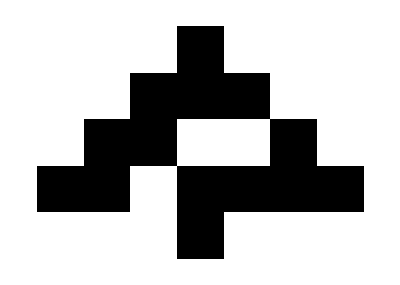

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

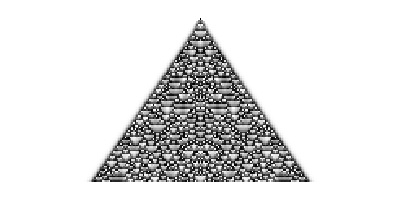

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
(*30 rule for 4 given steps*)
ca30= CellularAutomaton[30,{0,0,0,1,0,0,0},4];
ArrayPlot[ca30];
(*100 steps rule 30, with rand inital conditions*)
ca30init=CellularAutomaton[30,RandomInteger[1,250],100];
ArrayPlot[ca30init];
(*rule 30 evolving from init 1 black cell*)
ca30init1=CellularAutomaton[30,{{1,1},0},100];
ArrayPlot[ca30init1];
(*rule 30 evolving from init condition of a {1,1} seed on a background of repeated {1,0,1,1} blocks*)
ca30init11=CellularAutomaton[30,{{1,1},{1,0,1,1}},100];
ArrayPlot[ca30init11];

(*rule 30 with init offset*)
caOffset= CellularAutomaton[30,{{{{1},{-40}},{{1},{40}}},0},100];
ArrayPlot[caOffset];

(*tuple data type*)
Tuples[{1,0},3];
(*predicts cell color for each 8 neighborhoods*)
Map[CellularAutomaton[30,#,1][[2,2]]&,%];

(*rule with rule number 921408*)
ca92=CellularAutomaton[{921408,3,1},{{1},0},100];
ArrayPlot[ca92];

(*step number as 2nd arg, totalistic rules with k=3, r=1, code number 867*)
caT=CellularAutomaton[{867,{3,1},1},{{1},0},100];
ArrayPlot[caT];

(*ca additive rule adds modulo 4*)
caM4=CellularAutomaton[{Mod[Apply[Plus,#],4]&,{},1},{{1},0},100];
ArrayPlot[caM4];

(*{1,0} step argument given as second argument*)
ca2Arg=CellularAutomaton[{Mod[Total[#]+#2,4]&,{},1},{{1},0},100];
ArrayPlot[ca2Arg];

(*cells need not integer values*)
caNNOTINT=CellularAutomaton[{Mod[1/2 Apply[Plus,#],1]&,{},1},{{1},0},100];
ArrayPlot[caNNOTINT];

(*parametrically symbolic*)
s=Simplify[CellularAutomaton[{Mod[Apply[Plus,#],2]&,{},1},{{a},0},2],a∈Integers];
ArrayPlot[s];

(*evolves 100 steps caching every other step*)
ArrayPlot[CellularAutomaton[30,{{1},0},{{0,100,2}}]];

(*keeps all steps,but drops cells at offsets more than 20 on the left.*)
ArrayPlot[CellularAutomaton[30,{{1},0},{100,{-20,100}}]];
(* keeps the center column of cells ArrayPlot[CellularAutomaton[30,{{1},0},{20,{0}}]]*)

(*parts that are not constant black are kept*)
ArrayPlot[CellularAutomaton[225,{{1},0},100]];

(*Higher dimensional rules with 70 step*)
code797={797,{2,1},{1,1}};
ArrayPlot[First[CellularAutomaton[code797,{{{1}},0},{{70}}]]];

ArrayPlot[ca30]
ArrayPlot[ca30init]
ArrayPlot[ca30init1]
ArrayPlot[ca30init11]
ArrayPlot[caOffset]
ArrayPlot[ca92]
ArrayPlot[caT]
ArrayPlot[caM4]
ArrayPlot[ca2Arg]
ArrayPlot[caNNOTINT]
ArrayPlot[CellularAutomaton[30,{{1},0},{{0,100,2}}]]
ArrayPlot[CellularAutomaton[30,{{1},0},{{0,100,2}}]]
ArrayPlot[CellularAutomaton[30,{{1},0},{100,{-20,100}}]]
ArrayPlot[CellularAutomaton[225,{{1},0},100]]
ArrayPlot[First[CellularAutomaton[code797,{{{1}},0},{{70}}]]]
```